```mathematica
SetDirectory[NotebookDirectory[]];
fRandomFunction[x_,y_]:=PDF[MultinormalDistribution[{5,5},{{1,0.5},{0.5,1}}],{x,y}]
xTicks =Table[{i,100i},{i,2,10,2}];
fStep[aXOrY_Integer,aXOld_,aYOld_]:=Module[{aX,aY},If[aXOrY==1,aX=aXOld,aY=aYOld];If[aXOrY==1(*Means X is held constant*),aY=RandomVariate[ProbabilityDistribution[fRandomFunction[aXOld,y],{y,0,10}],{1}][[1]],aX=RandomVariate[ProbabilityDistribution[fRandomFunction[x,aYOld],{x,0,10}],{1}][[1]]]; {aX,aY}]
fStep1[aXOrY_Integer,{aXOld_,aYOld_}]:=Module[{aX,aY},If[aXOrY==1,aX=aXOld,aY=aYOld];If[aXOrY==1(*Means X is held constant*),aY=RandomVariate[ProbabilityDistribution[fRandomFunction[aXOld,y],{y,0,10}],{1}][[1]],aX=RandomVariate[ProbabilityDistribution[fRandomFunction[x,aYOld],{x,0,10}],{1}][[1]]]; {aX,aY}]
fStep2[{aXOrY_Integer,aXOld_,aYOld_}]:=Module[{aX,aY},If[aXOrY==1,aX=aXOld,aY=aYOld];If[aXOrY==1(*Means X is held constant*),aY=RandomVariate[ProbabilityDistribution[fRandomFunction[aXOld,y],{y,0,10}],{1}][[1]],aX=RandomVariate[ProbabilityDistribution[fRandomFunction[x,aYOld],{x,0,10}],{1}][[1]]]; {If[aXOrY==1,0,1],aX,aY}]
fStep3[{aXOrY_Integer,aXOld_,aYOld_}]:=Module[{aX,aY},If[aXOrY==1,aX=aXOld,aY=aYOld];If[aXOrY==1(*Means X is held constant*),aY=fConditionalNormalRand[aXOld],aX=fConditionalNormalRand[aYOld]]; {If[aXOrY==1,0,1],aX,aY}]
fConditionalNormalRand[aXOrY_]:=RandomVariate[NormalDistribution[5+0.5(aXOrY-5),1-0.5^2],{1}][[1]]
fRunGibbs[aNumSteps_Integer,aXStart_,aYStart_]:=NestList[fStep3[##]&,{1,aXStart,aYStart},aNumSteps][[All,2;;3]]
fSelectNewSite[aCurrentLocation_,aSigma_]:=Mod[aCurrentLocation+RandomVariate[MultinormalDistribution[{0,0},{{aSigma,0},{0,aSigma}}],1][[1]],10]
fStepMetropolis[aCurrentLocation_,aSigma_]:=Module[{aNewLocation=fSelectNewSite[aCurrentLocation,aSigma],aCurrentB=fRandomFunction@@aCurrentLocation,aNewB,r,p=RandomReal[]},aNewB=fRandomFunction@@aNewLocation; r=aNewB/aCurrentB; If[r>p,aNewLocation,aCurrentLocation]]
```

```mathematica
g1=Show[Plot3D[{fRandomFunction[x,y]},{x,0,10},{y,0,10},AxesLabel->{"East, km","North, km", ""},PlotRange->{Full,Full,{0,0.25}},ColorFunction->"BrassTones",Mesh->Automatic,MeshStyle->Blue,PlotPoints->20,Ticks->{xTicks,xTicks,None},ViewPoint->{1.4610778682878827,-1.9342706141474402,2.3608999669712687},ViewVertical->{0.,0.,1.}]]
```

-Graphics3D-

```mathematica
Export["Gibbs_goldMiningAgain1.png",g1]
```

Gibbs_goldMiningAgain1.png

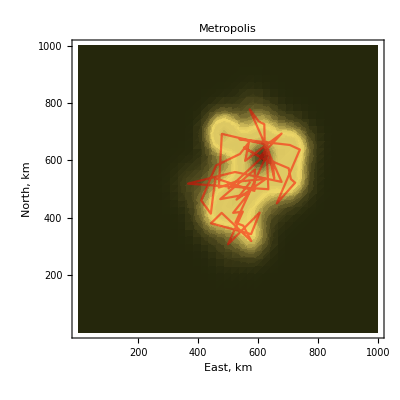

```mathematica
lSamplesMetropolis=NestList[fStepMetropolis[#,1]&,{5,5},100];
g2=Show[SmoothDensityHistogram[lSamplesMetropolis,Mesh->20,PlotRange->{{0,10},{0,10}},Frame->{True,True,False,False},PlotLabel->"Metropolis",FrameLabel->{"East, km","North, km"},FrameTicks->{xTicks,xTicks},ColorFunction->"BrassTones"],ListLinePlot[lSamplesMetropolis,PlotRange->{{0,10},{0,10}},PlotStyle->{Red,Opacity[0.5]}]]
```

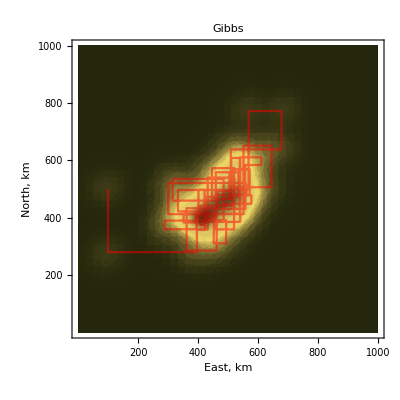

```mathematica
lSamples=fRunGibbs[100,1,5];
g3=Show[SmoothDensityHistogram[lSamples,Mesh->20,PlotRange->{{0,10},{0,10}},Frame->{True,True,False,False},PlotLabel->"Gibbs",FrameLabel->{"East, km","North, km"},FrameTicks->{xTicks,xTicks},ColorFunction->"BrassTones"],ListLinePlot[lSamples,PlotRange->{{0,10},{0,10}},PlotStyle->{Red,Opacity[0.5]}]]
```

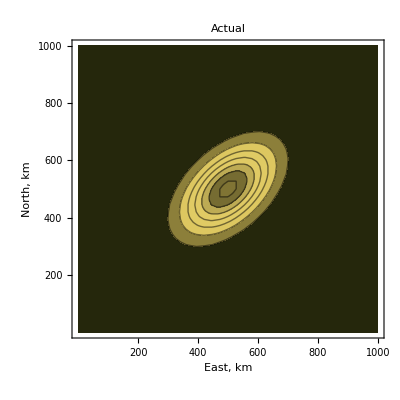

```mathematica
g1a=Show[ContourPlot[{fRandomFunction[y,x]},{x,0,10},{y,0,10},Frame->{True,True,False,False},FrameLabel->{"East, km","North, km", ""},PlotRange->{Full,Full,{0,0.25}},ColorFunction->"BrassTones",PlotPoints->20,FrameTicks->{xTicks,xTicks},PlotLabel->"Actual"]]
```

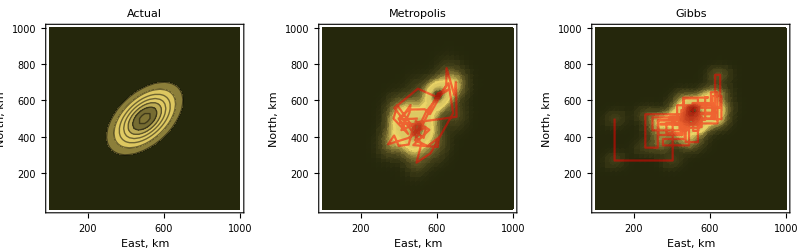

```mathematica
gFinal1=Show[GraphicsRow[{g1a,g2,g3}],ImageSize->800]
```

```mathematica
Export["Gibbs_goldMiningAgain2.png",gFinal1]
```

Gibbs_goldMiningAgain2.png

```mathematica
fPlotHistogram[lSample__]:=Show[Histogram3D[lSample,{0.25},"Probability",ChartStyle->{Opacity[1]},AxesLabel->{"East, km","North, km", ""},PlotRange->{{0,10},{0,10},Full},ColorFunction->"BrassTones",Ticks->{xTicks,xTicks,None},ViewPoint->{1.4610778682878827,-1.9342706141474402,2.3608999669712687},ViewVertical->{0.,0.,1.},PlotLabel->StringJoin["n = ",ToString[Length@lSample-1]]]]
```

```mathematica
nSampleSize={1000,10000,100000};
lSamplesGibbs=Table[fRunGibbs[nSampleSize[[i]],5,5],{i,1,3,1}];
lSamplesMetropolis=Table[NestList[fStepMetropolis[#,1]&,{5,5},nSampleSize[[i]]],{i,1,3,1}];
```

```mathematica
gFinal2=Show[GraphicsGrid[{{fPlotHistogram[lSamplesMetropolis[[1]]],fPlotHistogram[lSamplesGibbs[[1]]]},{fPlotHistogram[lSamplesMetropolis[[2]]],fPlotHistogram[lSamplesGibbs[[2]]]},{fPlotHistogram[lSamplesMetropolis[[3]]],fPlotHistogram[lSamplesGibbs[[3]]]}}],ImageSize->1200]
```

-Graphics-

```mathematica
Export["Gibbs_goldMiningAgain3.png",gFinal2]
```

Gibbs_goldMiningAgain3.png